```mathematica
(*Import[NotebookDirectory[]<>"myFunctionsandHamiltonianDefinitions.m"]*)
```

## Inicialize some functions

```mathematica
Remove["Global`*"]
```

```mathematica
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
compileOptionsPar={Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
```

## First order perturbation Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

```mathematica
nn=3;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

```mathematica
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];

M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

# N -> ∞

### Phase transitions

```mathematica
en0[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort},
enNonSort=Eigenvalues[HC[λ,χ],Method->{"Banded"}];
Sort[enNonSort]⟦1⟧
]
en1[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort},
enNonSort=Eigenvalues[HC[λ,χ],Method->{"Banded"}];
Sort[enNonSort]⟦2⟧
]
```

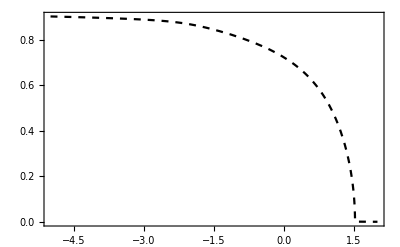

```mathematica
transMin3=Plot[χ/.Last@FindMaximum[{en0[λ,χ]-en1[λ,χ],χ>0},{χ,1}],{λ,-5,2},Evaluate@font,PlotPoints->30,Frame->True,Axes->False,PlotStyle->{Black,Dashed,Thickness[0.004]},PlotLegends->Automatic]
```

```mathematica
transAnal=ContourPlot[χ^2==(λ-1)/(λ-2),{λ,-5,2},{χ,-0,1},ContourStyle->Red,AspectRatio->6/10];
transline=ListLinePlot[{{1,0},{5,0}},PlotStyle->{Red,Thickness[0.004]}];
transP=ListPlot[{{1,0}},PlotStyle->{Blue,PointSize[Large]}];
```

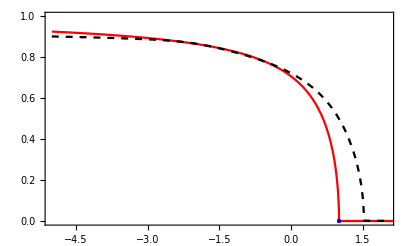

```mathematica
transCompare=Show[{transAnal,transline,transMin3,transP},ImageSize->410,Evaluate@font,FrameLabel->MaTeX/@{"\\lambda","\\chi"},ImageSize->410]
```

```mathematica
Export[NotebookDirectory[]<>"../dp_text/img/infiniteN_transitionCompare.pdf",transCompare]
```

/home/strelda/Documents/mff/dp/code/../dp_text/img/infiniteN_transitionCompare.pdf